```mathematica
(*How to calculate Differentiation Matrix Using Lagendre Polynomial*)
```

```mathematica
pp=LegendreP[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},τ]
```

{τ,1/2 (-1+3 τ^2),1/2 (-3 τ+5 τ^3),1/8 (3-30 τ^2+35 τ^4),1/8 (15 τ-70 τ^3+63 τ^5),1/16 (-5+105 τ^2-315 τ^4+231 τ^6),1/16 (-35 τ+315 τ^3-693 τ^5+429 τ^7),1/128 (35-1260 τ^2+6930 τ^4-12012 τ^6+6435 τ^8),1/128 (315 τ-4620 τ^3+18018 τ^5-25740 τ^7+12155 τ^9),1/256 (-63+3465 τ^2-30030 τ^4+90090 τ^6-109395 τ^8+46189 τ^10),1/256 (-693 τ+15015 τ^3-90090 τ^5+218790 τ^7-230945 τ^9+88179 τ^11),(231-18018 τ^2+225225 τ^4-1021020 τ^6+2078505 τ^8-1939938 τ^10+676039 τ^12)/1024,(3003 τ-90090 τ^3+765765 τ^5-2771340 τ^7+4849845 τ^9-4056234 τ^11+1300075 τ^13)/1024,(-429+45045 τ^2-765765 τ^4+4849845 τ^6-14549535 τ^8+22309287 τ^10-16900975 τ^12+5014575 τ^14)/2048,(-6435 τ+255255 τ^3-2909907 τ^5+14549535 τ^7-37182145 τ^9+50702925 τ^11-35102025 τ^13+9694845 τ^15)/2048,(6435-875160 τ^2+19399380 τ^4-162954792 τ^6+669278610 τ^8-1487285800 τ^10+1825305300 τ^12-1163381400 τ^14+300540195 τ^16)/32768}

```mathematica
pp[[1]]
```

τ

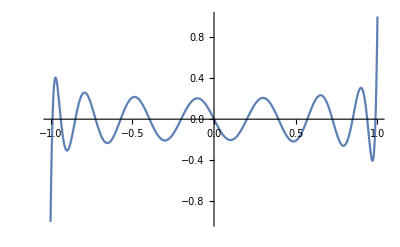

```mathematica
Plot[LegendreP[15,x],{x,-1,1}]
```

```mathematica
dp4=D[pp[[15]],τ]
```

(-6435+765765 τ^2-14549535 τ^4+101846745 τ^6-334639305 τ^8+557732175 τ^10-456326325 τ^12+145422675 τ^14)/2048

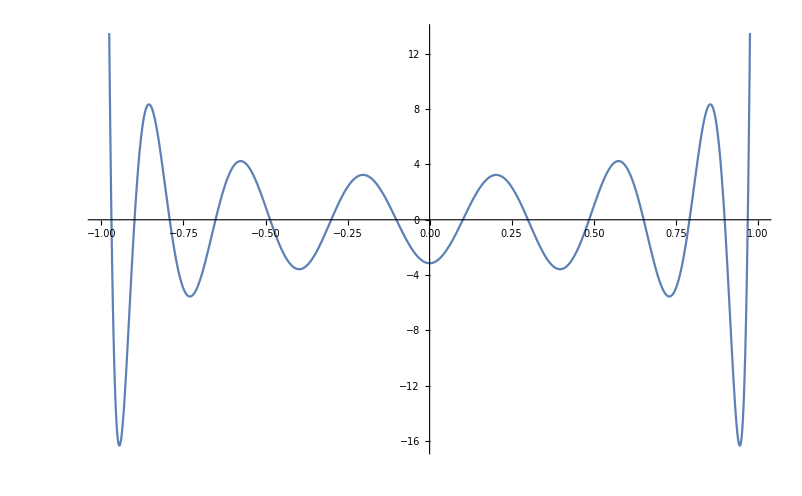

```mathematica
Plot[dp4,{τ,-1,1}]
```

```mathematica
tt1={FindRoot[dp4==0,{τ,0.1}],FindRoot[dp4==0,{τ,0.3}],FindRoot[dp4==0,{τ,0.5}],FindRoot[dp4==0,{τ,0.65}],FindRoot[dp4==0,{τ,0.8}],FindRoot[dp4==0,{τ,0.9}],FindRoot[dp4==0,{τ,1.0}]}
```

{{τ→0.101326},{τ→0.29983},{τ→0.486059},{τ→0.652389},{τ→0.792008},{τ→0.899201},{τ→0.969568}}

```mathematica
tt2={FindRoot[dp4==0,{τ,-0.1}],FindRoot[dp4==0,{τ,-0.3}],FindRoot[dp4==0,{τ,-0.5}],FindRoot[dp4==0,{τ,-0.65}],FindRoot[dp4==0,{τ,-0.8}],FindRoot[dp4==0,{τ,-0.9}],FindRoot[dp4==0,{τ,-1.0}]}
```

{{τ→-0.101326},{τ→-0.29983},{τ→-0.486059},{τ→-0.652389},{τ→-0.792008},{τ→-0.899201},{τ→-0.969568}}

```mathematica
nn=15;
```

```mathematica
τ1={-1,-0.9695680462702003,-0.8992005330934347, -0.7920082918618137,-0.6523887028824961,-0.48605942188713736,-0.29983046890076315,-0.10132627352194945,0.10132627352194945,0.29983046890076315,0.48605942188713736,0.6523887028824961,0.7920082918618137,0.8992005330934347,0.9695680462702003,1};
```

```mathematica
{-nn(nn+1)/4,nn(nn+1)/4}
```

{-60,60}

```mathematica
pp[[15]]
```

(-6435 τ+255255 τ^3-2909907 τ^5+14549535 τ^7-37182145 τ^9+50702925 τ^11-35102025 τ^13+9694845 τ^15)/2048

```mathematica
i=1;k=0;
{τ1[[i+1]],τ1[[k+1]]}
D10= (pp[[15]]/.(τ->  τ1[[k+1]]))/(pp[[15]]/.(τ-> τ1[[i+1]]))/(τ1[[k+1]]-τ1[[i+1]])
```

{-0.969568,-1}

81.1723

```mathematica
For[k=0,k<(nn+1),k++,
For[i=0,i<(nn+1),i++,
Which[
i==k==0,DiffD[i,k]=-nn(nn+1)/4,
i==k==nn,DiffD[i,k]=nn(nn+1)/4,
i==k,DiffD[i,k]=0.0,
i≠k,DiffD[i,k]=(pp[[nn]]/.(τ->  τ1[[k+1]]))/(pp[[nn]]/.(τ-> τ1[[i+1]]))/(τ1[[k+1]]-τ1[[i+1]])]
]]
Table[DiffD[i,k],{k,0,nn},{i,0,nn}]//MatrixForm

(*----------------------------------------------------------------------------------------------------------*)
```

(-60 | 81.1723 | -32.4927 | 18.5653 | -12.3679 | 8.97981 | -6.88559 | 5.47797 | -4.46998 | 3.70901 | -3.10559 | 2.60182 | -2.15481 | 1.72454 | -1.2542 | 1/2
-13.3025 | 0. | 18.8423 | -8.80372 | 5.48715 | -3.86401 | 2.91408 | -2.29532 | 1.86096 | -1.53748 | 1.28349 | -1.07303 | 0.887379 | -0.709498 | 0.515694 | -0.205538
3.02899 | -10.7182 | 0. | 10.9987 | -5.31838 | 3.41065 | -2.45587 | 1.88384 | -1.50227 | 1.22764 | -1.0172 | 0.845996 | -0.697119 | 0.556049 | -0.403588 | 0.160763
-1.2451 | 3.60284 | -7.91284 | 0. | 7.97433 | -3.90646 | 2.53673 | -1.84584 | 1.42712 | -1.1435 | 0.935143 | -0.770822 | 0.631307 | -0.501532 | 0.363152 | -0.144515
0.66914 | -1.81152 | 3.08666 | -6.43299 | 0. | 6.4539 | -3.18071 | 2.07793 | -1.51924 | 1.17766 | -0.942926 | 0.766414 | -0.621831 | 0.490996 | -0.35425 | 0.140766
-0.421606 | 1.10702 | -1.71777 | 2.73476 | -5.60068 | 0. | 5.60941 | -2.77257 | 1.81601 | -1.32924 | 1.02868 | -0.818269 | 0.654658 | -0.51231 | 0.367712 | -0.145809
0.296246 | -0.765048 | 1.13346 | -1.62735 | 2.52938 | -5.1403 | 0. | 5.14408 | -2.54544 | 1.66761 | -1.21807 | 0.9365 | -0.733577 | 0.566591 | -0.403641 | 0.159577
-0.226035 | 0.57793 | -0.83385 | 1.13566 | -1.58477 | 2.43668 | -4.93348 | 0. | 4.93455 | -2.44123 | 1.59601 | -1.15867 | 0.878037 | -0.664957 | 0.468565 | -0.184443
0.184443 | -0.468565 | 0.664957 | -0.878037 | 1.15867 | -1.59601 | 2.44123 | -4.93455 | 0. | 4.93348 | -2.43668 | 1.58477 | -1.13566 | 0.83385 | -0.57793 | 0.226035
-0.159577 | 0.403641 | -0.566591 | 0.733577 | -0.9365 | 1.21807 | -1.66761 | 2.54544 | -5.14408 | 0. | 5.1403 | -2.52938 | 1.62735 | -1.13346 | 0.765048 | -0.296246
0.145809 | -0.367712 | 0.51231 | -0.654658 | 0.818269 | -1.02868 | 1.32924 | -1.81601 | 2.77257 | -5.60941 | 0. | 5.60068 | -2.73476 | 1.71777 | -1.10702 | 0.421606
-0.140766 | 0.35425 | -0.490996 | 0.621831 | -0.766414 | 0.942926 | -1.17766 | 1.51924 | -2.07793 | 3.18071 | -6.4539 | 0. | 6.43299 | -3.08666 | 1.81152 | -0.66914
0.144515 | -0.363152 | 0.501532 | -0.631307 | 0.770822 | -0.935143 | 1.1435 | -1.42712 | 1.84584 | -2.53673 | 3.90646 | -7.97433 | 0. | 7.91284 | -3.60284 | 1.2451
-0.160763 | 0.403588 | -0.556049 | 0.697119 | -0.845996 | 1.0172 | -1.22764 | 1.50227 | -1.88384 | 2.45587 | -3.41065 | 5.31838 | -10.9987 | 0. | 10.7182 | -3.02899
0.205538 | -0.515694 | 0.709498 | -0.887379 | 1.07303 | -1.28349 | 1.53748 | -1.86096 | 2.29532 | -2.91408 | 3.86401 | -5.48715 | 8.80372 | -18.8423 | 0. | 13.3025
-1/2 | 1.2542 | -1.72454 | 2.15481 | -2.60182 | 3.10559 | -3.70901 | 4.46998 | -5.47797 | 6.88559 | -8.97981 | 12.3679 | -18.5653 | 32.4927 | -81.1723 | 60)